# Define Stokeslets

First we define the point source Greens functions

```mathematica
x = xo - xs;
y = yo - ys;
r = Sqrt[x^2 + y^2];
ux = fx/(2*π*η)*(-Log[r]+x^2/r^2) + fy/(2*π*η)*(x*y/r^2) ;
uy = fx/(2*π*η)*(x*y/r^2) + fy/(2*π*η)*(-Log[r]+y^2/r^2);
sxx = η *D[ux,xo]//Simplify
syy =  η D[uy,yo]//Simplify
sxy = η*D[ux,yo]/2+η*D[uy,xo]/2//Simplify
```

-((fx (xo-xs)+fy (yo-ys)) (xo^2-2 xo xs+xs^2-(yo-ys)^2))/(2 π (xo^2-2 xo xs+xs^2+(yo-ys)^2)^2)

((fx (xo-xs)+fy (yo-ys)) (xo^2-2 xo xs+xs^2-(yo-ys)^2))/(2 π (xo^2-2 xo xs+xs^2+(yo-ys)^2)^2)

-((xo-xs) (fx (xo-xs)+fy (yo-ys)) (yo-ys))/(π (xo^2-2 xo xs+xs^2+(yo-ys)^2)^2)

# Integrate point source over a line

Here we derive the general solutions for a Stokeslet in a full space integrated over the domain

#### Integrate displacement components

```mathematica
UXindef = Integrate[ux,ys,GeneratedParameters->C];
UXdef = ReplaceAll[UXindef,{ys->a}]-ReplaceAll[UXindef,{ys->-a}]//FullSimplify
UYindef = Integrate[uy,ys,GeneratedParameters->C];
UYdef = ReplaceAll[UYindef,{ys->a}]-ReplaceAll[UYindef,{ys->-a}]//FullSimplify
```

(4 a fx+(-a fx-fy xo+fy xs+fx yo) Log[(xo-xs)^2+(a-yo)^2]-(fy (-xo+xs)+fx (a+yo)) Log[(xo-xs)^2+(a+yo)^2])/(4 π η)

(8 a fy+4 fy (xo-xs) ArcTan[(xo-xs)/(a-yo)]+4 fy (xo-xs) ArcTan[(xo-xs)/(a+yo)]+(-a fy-fx xo+fx xs+fy yo) Log[(xo-xs)^2+(a-yo)^2]-(fx (-xo+xs)+fy (a+yo)) Log[(xo-xs)^2+(a+yo)^2])/(4 π η)

#### Integrate stress components

```mathematica
SXYindef = Integrate[sxy,ys,GeneratedParameters->C];
SXYdef = ReplaceAll[SXYindef,{ys->a}]-ReplaceAll[SXYindef,{ys->-a}]//FullSimplify

SXXindef = Integrate[sxx,ys,GeneratedParameters->C];
SXXdef = ReplaceAll[SXXindef,{ys->a}]-ReplaceAll[SXXindef,{ys->-a}]//FullSimplify

SYYindef = Integrate[syy,ys,GeneratedParameters->C];
SYYdef = ReplaceAll[SYYindef,{ys->a}]-ReplaceAll[SYYindef,{ys->-a}]//FullSimplify
```

((xo-xs) ((2 a (fy (a^2+(xo-xs)^2)+2 fx (-xo+xs) yo-fy yo^2))/(((xo-xs)^2+(a-yo)^2) ((xo-xs)^2+(a+yo)^2))-(fy (ArcTan[(a-yo)/(xo-xs)]+ArcTan[(a+yo)/(xo-xs)]))/(xo-xs)))/(2 π)

(-(4 a (xo-xs) (fx (a^2+(xo-xs)^2)+2 fy (xo-xs) yo-fx yo^2))/(((xo-xs)^2+(a-yo)^2) ((xo-xs)^2+(a+yo)^2))-fy Log[(xo-xs)^2+(a-yo)^2]+fy Log[(xo-xs)^2+(a+yo)^2])/(4 π)

((4 a (xo-xs) (fx (a^2+(xo-xs)^2)+2 fy (xo-xs) yo-fx yo^2))/(((xo-xs)^2+(a-yo)^2) ((xo-xs)^2+(a+yo)^2))+fy Log[(xo-xs)^2+(a-yo)^2]-fy Log[(xo-xs)^2+(a+yo)^2])/(4 π)

## Plot displacement components (u_x,u_y)

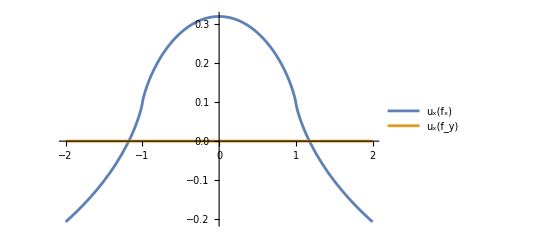

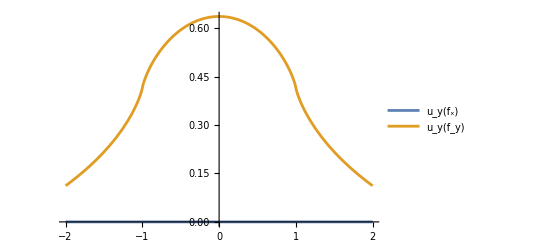

```mathematica
Plot[{ReplaceAll[UXdef,{fx -> 1,fy->0, η->1,a->1,xo->0.00001,xs->0}],
ReplaceAll[UXdef,{fx->0,fy->1,η->1,a->1,xo->0.00001,xs->0}]},
{yo,-2,2},PlotLegends->{"u_x(f_x)","u_x(f_y)"}]
Plot[{ReplaceAll[UYdef,{fx -> 1,fy->0, η->1,a->1,xo->0.00001,xs->0}],
ReplaceAll[UYdef,{fx->0,fy->1,η->1,a->1,xo->0.00001,xs->0}]},
{yo,-2,2},PlotLegends->{"u_y(f_x)","u_y(f_y)"}]
```

## Plot stress components (σ_xy,σ_xx,σ_yy)

The components  contain logarithmic singularities, while is discontinuous but non-singular. In the plot below, I plot each of the stress components at x = 0, which is where the source exists .

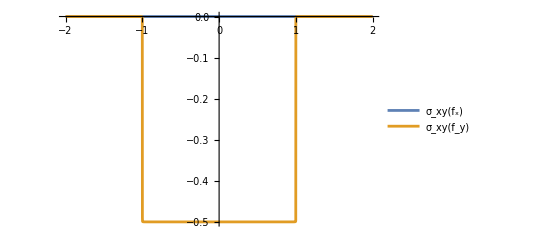

```mathematica
Plot[{ReplaceAll[SXYdef,{fx -> 1,fy->0, η->1,a->1,xo->0.00001,xs->0}],
ReplaceAll[SXYdef,{fx->0,fy->1,η->1,a->1,xo->0.00001,xs->0}]},
{yo,-2,2},PlotLegends->{"σ_xy(f_x)","σ_xy(f_y)"}]
```

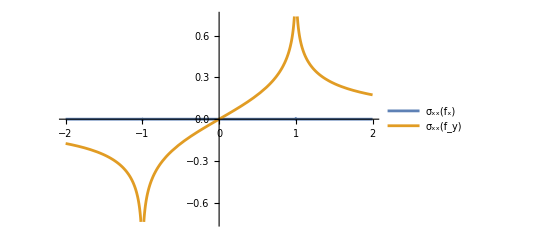

```mathematica
Plot[{ReplaceAll[SXXdef,{fx -> 1,fy->0, η->1,a->1,xo->0.00001,xs->0}],
ReplaceAll[SXXdef,{fx->0,fy->1,η->1,a->1,xo->0.00001,xs->0}]},
{yo,-2,2},PlotLegends->{"σ_xx(f_x)","σ_xx(f_y)"}]
```

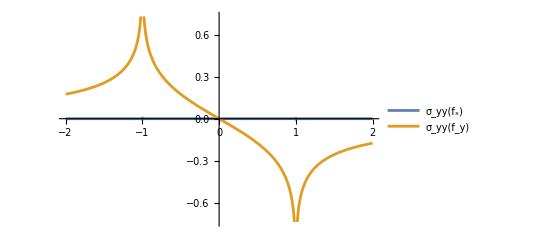

```mathematica
Plot[{ReplaceAll[SYYdef,{fx -> 1,fy->0, η->1,a->1,xo->0.00001,xs->0}],
ReplaceAll[SYYdef,{fx->0,fy->1,η->1,a->1,xo->0.00001,xs->0}]},
{yo,-2,2},PlotLegends->{"σ_yy(f_x)","σ_yy(f_y)"}]
```

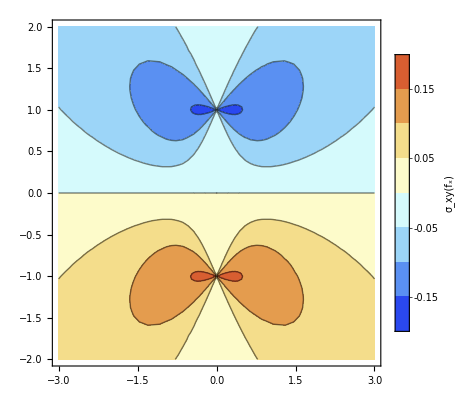
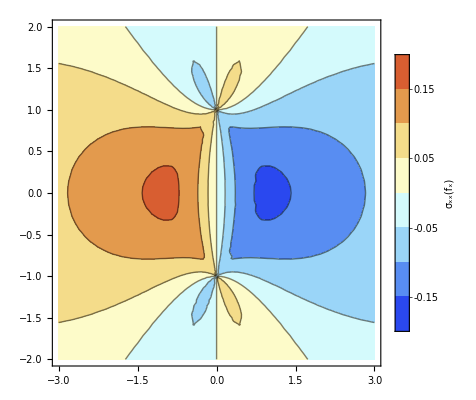
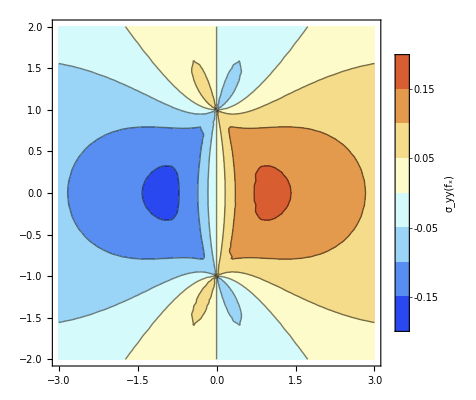

```mathematica
{ContourPlot[ReplaceAll[SXYdef,{fx -> 1,fy->0, η->1,a->1,xs->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σ_xy(f_x)"],ColorFunction->"LightTemperatureMap"],
ContourPlot[ReplaceAll[SXXdef,{fx->1,fy->-0,η->1,a->1,xs->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σ_xx(f_x)"],ColorFunction->"LightTemperatureMap"],
ContourPlot[ReplaceAll[SYYdef,{fx->1,fy->0,η->1,a->1,xs->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σ_yy(f_x)"],ColorFunction->"LightTemperatureMap"]}
```

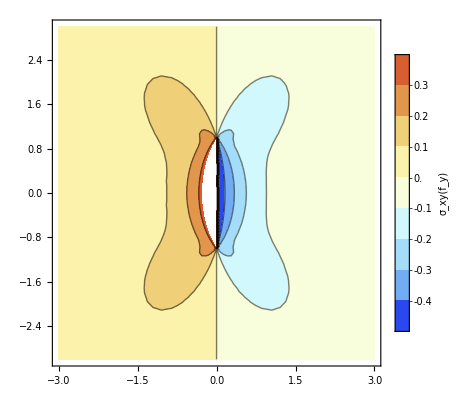
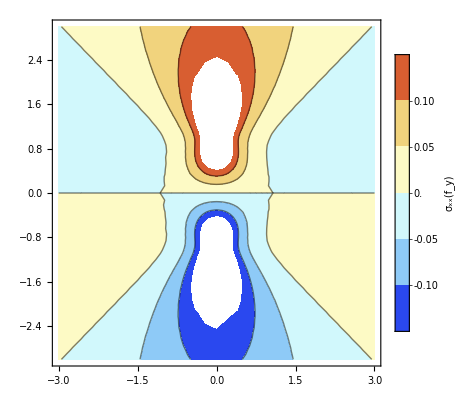
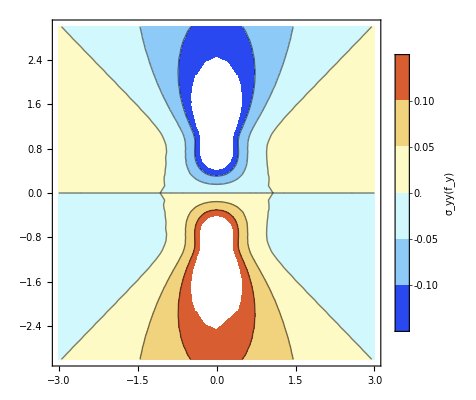

```mathematica
{ContourPlot[ReplaceAll[SXYdef,{fx -> 0,fy->1, η->1,a->1,xs->0}],{xo,-3,3},{yo,-3,3},PlotLegends->BarLegend[Automatic,LegendLabel->"σ_xy(f_y)"],ColorFunction->"LightTemperatureMap"],
ContourPlot[ReplaceAll[SXXdef,{fx->0,fy->1,η->1,a->1,xs->0}],{xo,-3,3},{yo,-3,3},PlotLegends->BarLegend[Automatic,LegendLabel->"σ_xx(f_y)"],ColorFunction->"LightTemperatureMap"],
ContourPlot[ReplaceAll[SYYdef,{fx->0,fy->1,η->1,a->1,xs->0}],{xo,-3,3},{yo,-3,3},PlotLegends->BarLegend[Automatic,LegendLabel->"σ_yy(f_y)"],ColorFunction->"LightTemperatureMap"]}
```